```mathematica
Quit
```

```mathematica
SetDirectory["~/Documents/Univ/Palatini"];
```

```mathematica
$Assumptions={β>0,γ>0};
```

```mathematica
E^3.044/10^10
```

2.0989×10^-9

```mathematica
Mpl=2.435 10^18;
```

```mathematica
ϕanal[NN_]=Sqrt[6/γ](3Sqrt[γ^(3/2)/(2β)]NN)^(2/3)//Simplify
dotϕanal[NN_]=-Sqrt[6/γ]Sqrt[6 β/γ^(3/2)Sqrt[γ/6]ϕanal[NN]]//Simplify
Hanal[NN_]=Sqrt[3] β/γ^(3/2)Sqrt[γ/6]ϕanal[NN]//Simplify
```

(3 6^(1/6) NN^(2/3))/β^(1/3)

-(3 2^(5/6) 3^(1/3) (NN β)^(1/3))/γ

(3 3^(1/6) (NN β)^(2/3))/(2^(1/3) γ)

```mathematica
ϵanal[NN_]=2/(3NN);
csanal[NN_]=1/Sqrt[18NN];
calPanal[NN_]=1/(2ϵanal[NN]csanal[NN])(Hanal[NN]/(2π))^2//Simplify
```

(81 3^(1/3) NN^(17/6) β^(4/3))/(16 2^(1/6) π^2 γ^2)

```mathematica
γanal[β_]=γ/.Solve[calPanal[70]==2 10^-9,γ][[2]]
```

(1575000 2^(1/3) 3^(1/6) 5^(11/12) 7^(5/12) β^(2/3))/π

```mathematica
P[X_]=-KK X+1/Mpl^4 X^2;
Xbar=KK Mpl^4/2;
```

```mathematica
P'[Xbar]
```

0

```mathematica
rho[X_]=2X P'[X]-P[X]//Simplify
```

X (-KK+(3 X)/Mpl^4)

```mathematica
rho[Xbar]//Simplify
```

(KK^2 Mpl^4)/4

```mathematica
Normal[Series[rho[Xbar+dX]+P[Xbar+dX],{dX,0,1}]]
```

2 dX KK

```mathematica
rhodot[X_]=(-Sqrt[3])/Mpl Sqrt[rho[X]](rho[X]+P[X])//Simplify
```

(2 (KK Mpl^4-2 X) X √(-3 KK X+(9 X^2)/Mpl^4))/Mpl^5

```mathematica
Simplify[Normal[Series[rhodot[Xbar+dX],{dX,0,1}]],{KK>0}]
```

-√3 dX KK^2 Mpl

```mathematica
-4 Sqrt[3]/Mpl^5 Xbar Sqrt[rho[Xbar]]//Simplify
```

-√3 KK √(KK^2) Mpl

## SO(1,1)

### trial

```mathematica
P[ϕ_,X_]=-β Tanh[ϕ/(√6)]X+γ^2/36 X^2;
PX[ϕ_,X_]=D[P[ϕ,X], X];
PXX[ϕ_,X_]=D[PX[ϕ,X], X];
Pϕ[ϕ_,X_]=D[P[ϕ,X], ϕ];
H[ϕ_,X_]=Sqrt[(2X PX[ϕ,X]-P[ϕ,X])/3];
dotH[ϕ_,X_]=-X PX[ϕ,X]//Simplify;
cs[ϕ_,X_]=Sqrt[PX[ϕ,X]/(PX[ϕ,X]+2X PXX[ϕ,X])];
p[ϕ_,dotϕ_,ddotϕ_]=D[PX[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]PX[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
ϵ[ϕ_,X_]=(-dotH[ϕ,X])/H[ϕ,X]^2//Simplify;
w[ϕ_,X_]=2/3 ϵ[ϕ,X]-1;
η[ϕ_,dotϕ_,ddotϕ_]=D[ϵ[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]ϵ[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
s[ϕ_,dotϕ_,ddotϕ_]=D[cs[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]cs[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
```

```mathematica
9/2 100^2
```

45000

```mathematica
R=1;
```

```mathematica
βs=10^6;
```

```mathematica
params={β->βs,γ->Sqrt[R]γanal[βs]};params//N
```

{β→1.×10^6,γ→7.51706×10^10}

```mathematica
Ni=200;
```

```mathematica
Hanal[Ni]/.{γ->Sqrt[R]γanal[β]}//N
ϕanal[Ni]/.params//N
```

0.0000130098

1.38303

```mathematica
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params;
```

```mathematica
tf=10^4 Hanal[Ni]^-1/.params;tf//N
```

7.68652×10^8

```mathematica
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf}][[1]]
```

{ϕ[t]→InterpolatingFunction[…][t],ϕ'[t]→InterpolatingFunction[…][t],ϕ''[t]→InterpolatingFunction[…][t],NN[t]→InterpolatingFunction[…][t]}

```mathematica
Mpl=2.435 10^18;
```

```mathematica
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
```

```mathematica
tend=t/.FindRoot[ϵsol[t]==1,{t,Ni Hanal[Ni]^-1/.params}]
```

4.11994×10^7

```mathematica
Nend=Nsol[tend]
```

196.509

```mathematica
Npivot=Nend-70
```

126.509

```mathematica
tpivot=t/.FindRoot[Nsol[t]==Npivot,{t,20 Hanal[Ni]^-1/.params}]
```

1.40351×10^7

```mathematica
nsm1sol[tpivot]+1
rsol[tpivot]
cssol[tpivot]
```

0.959041

0.00402734

0.0275996

```mathematica
R=calPsol[tpivot]/(2 10^-9)
```

1.

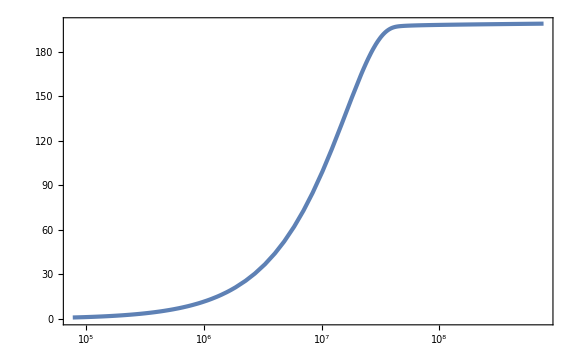

```mathematica
LogLinearPlot[Nsol[t],{t,Hanal[Ni]^-1/.params,tf}]
```

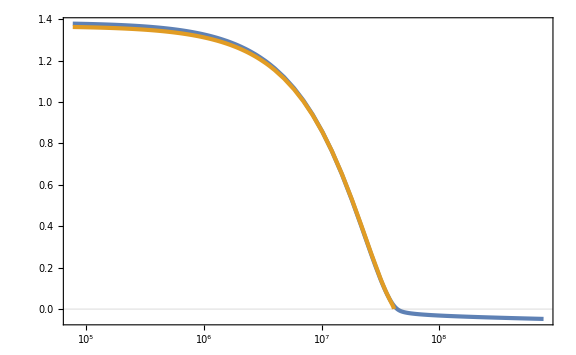

```mathematica
LogLinearPlot[{ϕsol[t],ϕanal[Nend-Nsol[t]]/.params},{t,Hanal[Ni]^-1/.params,tf},GridLines->{None,{0}}]
```

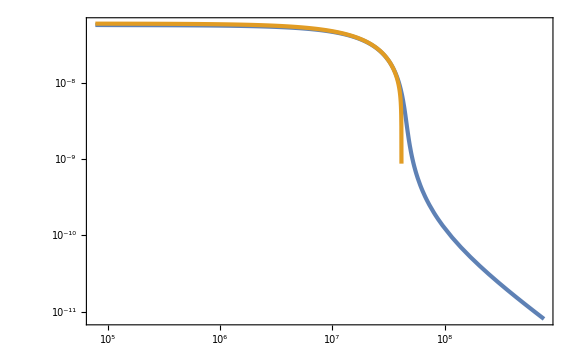

```mathematica
LogLogPlot[{-dotϕsol[t],-dotϕanal[Nend-Nsol[t]]/.params},{t,Hanal[Ni]^-1/.params,tf},PlotRange->Full]
```

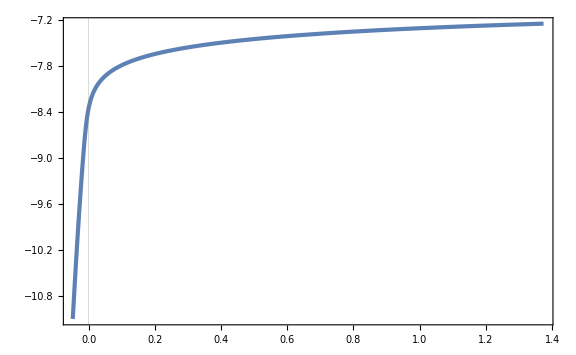

```mathematica
ParametricPlot[{ϕsol[t],Log10[Abs[dotϕsol[t]]]},{t,2 Hanal[Ni]^-1/.params,tf},PlotRange->Full,GridLines->{{0},None}]
```

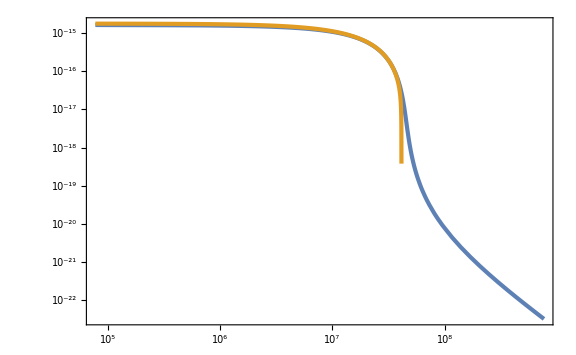

```mathematica
LogLogPlot[{dotϕsol[t]^2/2,dotϕanal[Nend-Nsol[t]]^2/2/.params},{t,Hanal[Ni]^-1/.params,tf},PlotRange->Full]
```

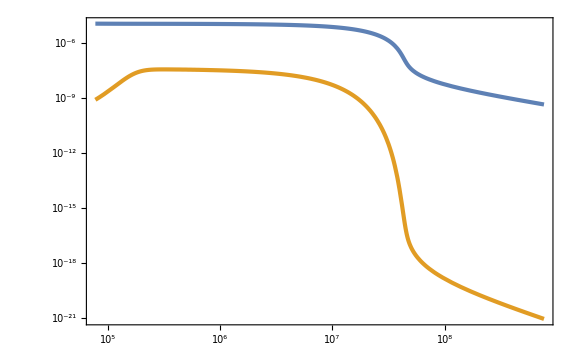

```mathematica
LogLogPlot[{Hsol[t],calPsol[t]},{t,Hanal[Ni]^-1/.params,tf}]
```

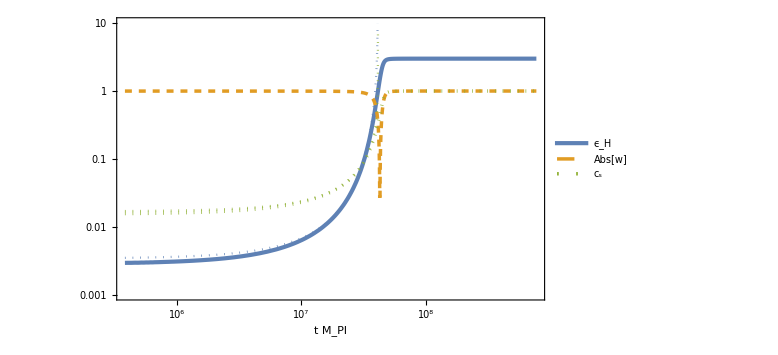

```mathematica
LogLogPlot[{ϵsol[t],ϵanal[Nend-Nsol[t]]/.params,Abs[wsol[t]],cssol[t],csanal[Nend-Nsol[t]]/.params(*,ηsol[t],1/(Nend-Nsol[t]),ssol[t],1/(2(Nend-Nsol[t]))*)},{t,5 Hanal[Ni]^-1/.params,tf},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],Dashed,AbsoluteThickness[2.5]},{Color[3],Dotted,AbsoluteThickness[2.5]},{Color[3],Dotted},{Color[4],AbsoluteThickness[3]},{Color[4],Dotted},{Color[5],AbsoluteThickness[3]},{Color[5],Dotted}},PlotRange->{10^-3,10},FrameLabel->{Subscript[M, Pl] t,None},PlotLegends->Placed[{Subscript[ϵ, H],None,Abs[w],Subscript[c, "s"]},{0.85,0.3}]]
```

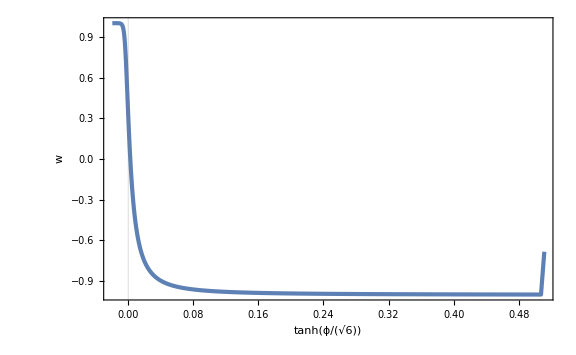

```mathematica
ParametricPlot[{Tanh[ϕsol[t]/Sqrt[6]],wsol[t]},{t,0,tf},PlotRange->Full,FrameLabel->{Tanh[ϕ/Sqrt[6]],w},GridLines->{{0},None}]
```

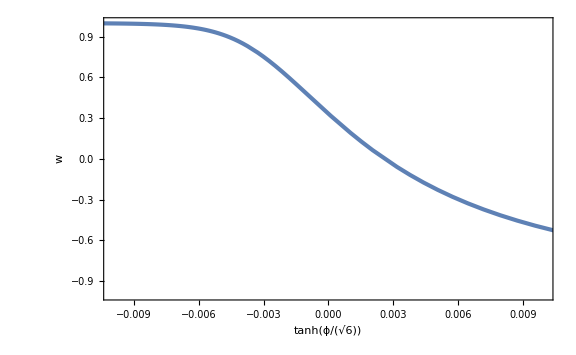

```mathematica
ParametricPlot[{Tanh[ϕsol[t]/Sqrt[6]],wsol[t]},{t,0,tf},FrameLabel->{Tanh[ϕ/Sqrt[6]],w},GridLines->{{0},{1/3}},PlotRange->{{-10^-2,10^-2},{-1,1}}]
```

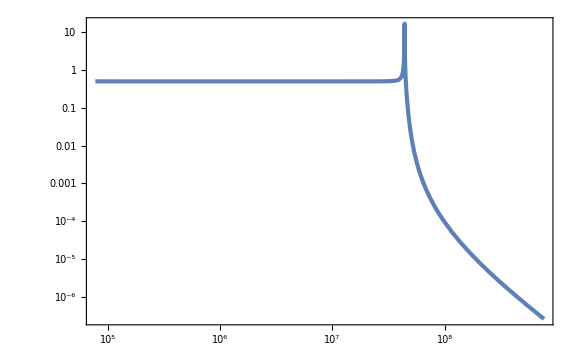

```mathematica
LogLogPlot[(Abs[β Tanh[ϕsol[t]/Sqrt[6]] dotϕsol[t]^2/2]/(γ^2/36(dotϕsol[t]^2/2)^2))^-1/.params,{t,Hanal[Ni]^-1/.params,tf}]
```

```mathematica
β/(γ^2/36)/.params
```

6.37099×10^-15

```mathematica
wList=Select[Table[{Nsol[t],wsol[t]},{t,0,tf,Hanal[Ni]^-1/.params}],#[[1]]>90&];
```

```mathematica
fitparam=FindFit[wList,Tanh[(2(x-a))/b],{{a,100},{b,1}},x]
```

{a→117.724,b→1.02351}

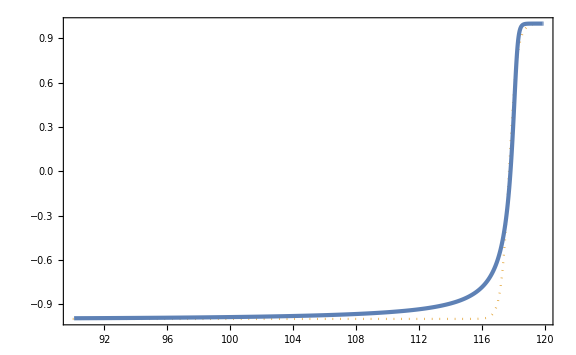

```mathematica
Show[Plot[Tanh[(2(x-a))/b]/.fitparam,{x,90,Nsol[tf]},PlotStyle->{Color[2],Dotted},PlotRange->Full],ListPlot[wList,PlotRange->Full]]
```

```mathematica
LogHList=Select[Table[{Nsol[t],Log10[Hsol[t]]},{t,0,tf,Hanal[Ni]^-1/.params}],#[[1]]>90&];
```

```mathematica
Hfit[NN_]=Log10[Exp[-3/2(NN-a+b/2(Log[Cosh[2(NN-a)/b]]+Log[2]))]]+log10H0/.fitparam//Simplify
```

log10H0+Log[(2.87723×10^76 ⅇ^(-3 NN/2))/Cosh[230.04-1.95407 NN]^0.767629]/Log[10]

```mathematica
H0fit=FindFit[LogHList,Hfit[NN],log10H0,NN]
```

{log10H0→-7.37998}

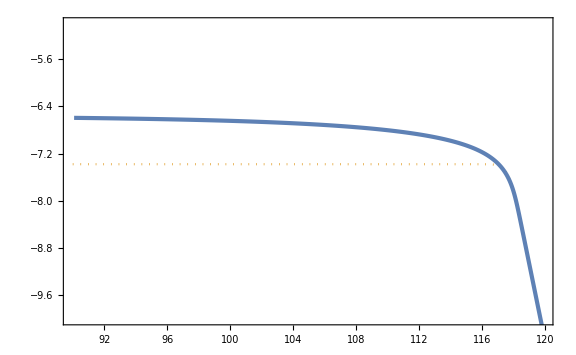

```mathematica
Show[Plot[Hfit[NN]/.H0fit,{NN,90,Nsol[tf]},PlotStyle->{Color[2],Dotted},PlotRange->{-10,-5}],ListPlot[LogHList,PlotRange->Full]]
```

```mathematica
H0dt=NIntegrate[10^(Hfit[NN]-log10H0)/.fitparam,{NN,a-b/.fitparam,a+b/.fitparam}]
```

1.13059

```mathematica
Ts=(2 30^(1/4))/Sqrt[3π] 106.75/106.75^(1/2)0.02 10^(2log10H0)Mpl/.H0fit
```

1333.27

```mathematica
67.3-Log[0.002/(67.4 10^3/299792458)]+1/3 Log[rsol[tpivot]/0.12]-1/3 Log[Ts/10^9]-1/12 Log[106.75]
```

66.0128

### recursion

```mathematica
P[ϕ_,X_]=-β Tanh[ϕ/(√6)]X+γ^2/36 X^2;
PX[ϕ_,X_]=D[P[ϕ,X], X];
PXX[ϕ_,X_]=D[PX[ϕ,X], X];
Pϕ[ϕ_,X_]=D[P[ϕ,X], ϕ];
H[ϕ_,X_]=Sqrt[(2X PX[ϕ,X]-P[ϕ,X])/3];
dotH[ϕ_,X_]=-X PX[ϕ,X]//Simplify;
cs[ϕ_,X_]=Sqrt[PX[ϕ,X]/(PX[ϕ,X]+2X PXX[ϕ,X])];
p[ϕ_,dotϕ_,ddotϕ_]=D[PX[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]PX[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
ϵ[ϕ_,X_]=(-dotH[ϕ,X])/H[ϕ,X]^2//Simplify;
w[ϕ_,X_]=2/3 ϵ[ϕ,X]-1;
η[ϕ_,dotϕ_,ddotϕ_]=D[ϵ[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]ϵ[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
s[ϕ_,dotϕ_,ddotϕ_]=D[cs[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]cs[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
```

```mathematica
9/2 74^2
```

24642

```mathematica
Ni=200;
Nms=60;
Nps=70;
```

```mathematica
DataList=Table[βs=10^logβs;
params={β->βs,γ->γanal[βs]};
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params;
tf=10^4 Hanal[Ni]^-1/.params;
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
tend=t/.FindRoot[ϵsol[t]==1,{t,Ni Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Nend=Nsol[tend];
Nm=Nend-Nms;
Np=Nend-Nps;
tm=t/.FindRoot[Nsol[t]==Nm,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsol[t]==Np,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Rm=calPsol[tm]/(2 10^-9);
Rp=calPsol[tp]/(2 10^-9);
paramsm={β->βs,γ->Sqrt[Rm]γanal[βs]};
paramsp={β->βs,γ->Sqrt[Rp]γanal[βs]};
EoMsm={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsm;
EoMsp={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsp;
tfm=10^4 Hanal[Ni]^-1/.paramsm;
tfp=10^4 Hanal[Ni]^-1/.paramsp;
solm=NDSolve[EoMsm,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfm},WorkingPrecision->30][[1]]//Quiet;
solp=NDSolve[EoMsp,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfp},WorkingPrecision->30][[1]]//Quiet;
ϕsolm[t_]=ϕ[t]/.solm;
dotϕsolm[t_]=ϕ'[t]/.solm;
ddotϕsolm[t_]=ϕ''[t]/.solm;
Nsolm[t_]=NN[t]/.solm;
Hsolm[t_]=H[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ϵsolm[t_]=ϵ[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
wsolm[t_]=w[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ηsolm[t_]=η[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
ssolm[t_]=s[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
cssolm[t_]=cs[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
calPsolm[t_]=1/(2ϵsolm[t] cssolm[t])(Hsolm[t]/(2π))^2;
nsm1solm[t_]=-2ϵsolm[t]-ηsolm[t]-ssolm[t];
rsolm[t_]=16ϵsolm[t]cssolm[t];
ϕsolp[t_]=ϕ[t]/.solp;
dotϕsolp[t_]=ϕ'[t]/.solp;
ddotϕsolp[t_]=ϕ''[t]/.solp;
Nsolp[t_]=NN[t]/.solp;
Hsolp[t_]=H[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ϵsolp[t_]=ϵ[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
wsolp[t_]=w[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ηsolp[t_]=η[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
ssolp[t_]=s[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
cssolp[t_]=cs[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
calPsolp[t_]=1/(2ϵsolp[t] cssolp[t])(Hsolp[t]/(2π))^2;
nsm1solp[t_]=-2ϵsolp[t]-ηsolp[t]-ssolp[t];
rsolp[t_]=16ϵsolp[t]cssolp[t];
tendm=t/.FindRoot[ϵsolm[t]==1,{t,Ni Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tendp=t/.FindRoot[ϵsolp[t]==1,{t,Ni Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
Nendm=Nsolm[tendm];
Nendp=Nsolp[tendp];
Nm=Nendm-Nms;
Np=Nendp-Nps;
tm=t/.FindRoot[Nsolm[t]==Nm,{t,20 Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsolp[t]==Np,{t,20 Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
{βs,nsm1solm[tm],rsolm[tm],cssolm[tm],nsm1solp[tp],rsolp[tp],cssolp[tp]},{logβs,3,10,1/10}];//AbsoluteTiming
```

{310.644,Null}

```mathematica
Export["nsrcs6070.dat",DataList];
```

```mathematica
DataList=Import["nsrcs6070.dat"]//ToExpression;
```

```mathematica
9/2 70^2
```

22050

```mathematica
10Log10[9/2 70^2/1000]//N
```

13.4341

```mathematica
PlanckBAO1s=Import["Planck2018_BAO_1sigma.dat"];
PlanckBAO2s=Import["Planck2018_BAO_2sigma.dat"];
PlanckBK1s=Import["Planck2018_BK_1sigma.dat"];
PlanckBK2s=Import["Planck2018_BK_2sigma.dat"];
```

```mathematica
PlanckBAO1sEx=Join[{{(1+10^-10)First[PlanckBAO1s][[1]],10^-10}},PlanckBAO1s,{{(1-10^-10)Last[PlanckBAO1s][[1]],10^-10}}];
PlanckBAO2sEx=Join[{{(1+10^-10)First[PlanckBAO2s][[1]],10^-10}},PlanckBAO2s,{{(1-10^-10)Last[PlanckBAO2s][[1]],10^-10}}];
PlanckBK1sEx=Join[{{(1+10^-10)First[PlanckBK1s][[1]],10^-10}},PlanckBK1s,{{(1-10^-10)Last[PlanckBK1s][[1]],10^-10}}];
PlanckBK2sEx=Join[{{(1+10^-10)First[PlanckBK2s][[1]],10^-10}},PlanckBK2s,{{(1-10^-10)Last[PlanckBK2s][[1]],10^-10}}];
```

```mathematica
nsrm=Table[{DataList[[i,2]]+1,DataList[[i,3]]},{i,Length[DataList]}];
nsrp=Table[{DataList[[i,5]]+1,DataList[[i,6]]},{i,Length[DataList]}];
```

```mathematica
Data20000={βs=20000;
params={β->βs,γ->γanal[βs]};
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params;
tf=10^4 Hanal[Ni]^-1/.params;
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
tend=t/.FindRoot[ϵsol[t]==1,{t,Ni Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Nend=Nsol[tend];
Nm=Nend-Nms;
Np=Nend-Nps;
tm=t/.FindRoot[Nsol[t]==Nm,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsol[t]==Np,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Rm=calPsol[tm]/(2 10^-9);
Rp=calPsol[tp]/(2 10^-9);
paramsm={β->βs,γ->Sqrt[Rm]γanal[βs]};
paramsp={β->βs,γ->Sqrt[Rp]γanal[βs]};
EoMsm={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsm;
EoMsp={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsp;
tfm=10^4 Hanal[Ni]^-1/.paramsm;
tfp=10^4 Hanal[Ni]^-1/.paramsp;
solm=NDSolve[EoMsm,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfm},WorkingPrecision->30][[1]]//Quiet;
solp=NDSolve[EoMsp,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfp},WorkingPrecision->30][[1]]//Quiet;
ϕsolm[t_]=ϕ[t]/.solm;
dotϕsolm[t_]=ϕ'[t]/.solm;
ddotϕsolm[t_]=ϕ''[t]/.solm;
Nsolm[t_]=NN[t]/.solm;
Hsolm[t_]=H[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ϵsolm[t_]=ϵ[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
wsolm[t_]=w[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ηsolm[t_]=η[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
ssolm[t_]=s[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
cssolm[t_]=cs[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
calPsolm[t_]=1/(2ϵsolm[t] cssolm[t])(Hsolm[t]/(2π))^2;
nsm1solm[t_]=-2ϵsolm[t]-ηsolm[t]-ssolm[t];
rsolm[t_]=16ϵsolm[t]cssolm[t];
ϕsolp[t_]=ϕ[t]/.solp;
dotϕsolp[t_]=ϕ'[t]/.solp;
ddotϕsolp[t_]=ϕ''[t]/.solp;
Nsolp[t_]=NN[t]/.solp;
Hsolp[t_]=H[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ϵsolp[t_]=ϵ[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
wsolp[t_]=w[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ηsolp[t_]=η[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
ssolp[t_]=s[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
cssolp[t_]=cs[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
calPsolp[t_]=1/(2ϵsolp[t] cssolp[t])(Hsolp[t]/(2π))^2;
nsm1solp[t_]=-2ϵsolp[t]-ηsolp[t]-ssolp[t];
rsolp[t_]=16ϵsolp[t]cssolp[t];
tendm=t/.FindRoot[ϵsolm[t]==1,{t,Ni Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tendp=t/.FindRoot[ϵsolp[t]==1,{t,Ni Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
Nendm=Nsolm[tendm];
Nendp=Nsolp[tendp];
Nm=Nendm-Nms;
Np=Nendp-Nps;
tm=t/.FindRoot[Nsolm[t]==Nm,{t,20 Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsolp[t]==Np,{t,20 Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
{βs,nsm1solm[tm],rsolm[tm],cssolm[tm],nsm1solp[tp],rsolp[tp],cssolp[tp]}}[[1]];
```

```mathematica
Export["nsrcs6070beta20000.dat",Data20000];
```

```mathematica
Data30000={βs=30000;
params={β->βs,γ->γanal[βs]};
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params;
tf=10^4 Hanal[Ni]^-1/.params;
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
tend=t/.FindRoot[ϵsol[t]==1,{t,Ni Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Nend=Nsol[tend];
Nm=Nend-Nms;
Np=Nend-Nps;
tm=t/.FindRoot[Nsol[t]==Nm,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsol[t]==Np,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Rm=calPsol[tm]/(2 10^-9);
Rp=calPsol[tp]/(2 10^-9);
paramsm={β->βs,γ->Sqrt[Rm]γanal[βs]};
paramsp={β->βs,γ->Sqrt[Rp]γanal[βs]};
EoMsm={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsm;
EoMsp={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsp;
tfm=10^4 Hanal[Ni]^-1/.paramsm;
tfp=10^4 Hanal[Ni]^-1/.paramsp;
solm=NDSolve[EoMsm,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfm},WorkingPrecision->30][[1]]//Quiet;
solp=NDSolve[EoMsp,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfp},WorkingPrecision->30][[1]]//Quiet;
ϕsolm[t_]=ϕ[t]/.solm;
dotϕsolm[t_]=ϕ'[t]/.solm;
ddotϕsolm[t_]=ϕ''[t]/.solm;
Nsolm[t_]=NN[t]/.solm;
Hsolm[t_]=H[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ϵsolm[t_]=ϵ[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
wsolm[t_]=w[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ηsolm[t_]=η[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
ssolm[t_]=s[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
cssolm[t_]=cs[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
calPsolm[t_]=1/(2ϵsolm[t] cssolm[t])(Hsolm[t]/(2π))^2;
nsm1solm[t_]=-2ϵsolm[t]-ηsolm[t]-ssolm[t];
rsolm[t_]=16ϵsolm[t]cssolm[t];
ϕsolp[t_]=ϕ[t]/.solp;
dotϕsolp[t_]=ϕ'[t]/.solp;
ddotϕsolp[t_]=ϕ''[t]/.solp;
Nsolp[t_]=NN[t]/.solp;
Hsolp[t_]=H[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ϵsolp[t_]=ϵ[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
wsolp[t_]=w[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ηsolp[t_]=η[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
ssolp[t_]=s[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
cssolp[t_]=cs[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
calPsolp[t_]=1/(2ϵsolp[t] cssolp[t])(Hsolp[t]/(2π))^2;
nsm1solp[t_]=-2ϵsolp[t]-ηsolp[t]-ssolp[t];
rsolp[t_]=16ϵsolp[t]cssolp[t];
tendm=t/.FindRoot[ϵsolm[t]==1,{t,Ni Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tendp=t/.FindRoot[ϵsolp[t]==1,{t,Ni Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
Nendm=Nsolm[tendm];
Nendp=Nsolp[tendp];
Nm=Nendm-Nms;
Np=Nendp-Nps;
tm=t/.FindRoot[Nsolm[t]==Nm,{t,20 Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsolp[t]==Np,{t,20 Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
{βs,nsm1solm[tm],rsolm[tm],cssolm[tm],nsm1solp[tp],rsolp[tp],cssolp[tp]}}[[1]];
```

```mathematica
Export["nsrcs6070beta30000.dat",Data30000];
```

```mathematica
Data50000={βs=50000;
params={β->βs,γ->γanal[βs]};
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params;
tf=10^4 Hanal[Ni]^-1/.params;
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
tend=t/.FindRoot[ϵsol[t]==1,{t,Ni Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Nend=Nsol[tend];
Nm=Nend-Nms;
Np=Nend-Nps;
tm=t/.FindRoot[Nsol[t]==Nm,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsol[t]==Np,{t,20 Hanal[Ni]^-1/.params},WorkingPrecision->30]//Quiet;
Rm=calPsol[tm]/(2 10^-9);
Rp=calPsol[tp]/(2 10^-9);
paramsm={β->βs,γ->Sqrt[Rm]γanal[βs]};
paramsp={β->βs,γ->Sqrt[Rp]γanal[βs]};
EoMsm={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsm;
EoMsp={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[Ni],ϕ'[0]==dotϕanal[Ni],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.paramsp;
tfm=10^4 Hanal[Ni]^-1/.paramsm;
tfp=10^4 Hanal[Ni]^-1/.paramsp;
solm=NDSolve[EoMsm,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfm},WorkingPrecision->30][[1]]//Quiet;
solp=NDSolve[EoMsp,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tfp},WorkingPrecision->30][[1]]//Quiet;
ϕsolm[t_]=ϕ[t]/.solm;
dotϕsolm[t_]=ϕ'[t]/.solm;
ddotϕsolm[t_]=ϕ''[t]/.solm;
Nsolm[t_]=NN[t]/.solm;
Hsolm[t_]=H[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ϵsolm[t_]=ϵ[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
wsolm[t_]=w[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
ηsolm[t_]=η[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
ssolm[t_]=s[ϕsolm[t],dotϕsolm[t],ddotϕsolm[t]]/.paramsm;
cssolm[t_]=cs[ϕsolm[t],dotϕsolm[t]^2/2]/.paramsm;
calPsolm[t_]=1/(2ϵsolm[t] cssolm[t])(Hsolm[t]/(2π))^2;
nsm1solm[t_]=-2ϵsolm[t]-ηsolm[t]-ssolm[t];
rsolm[t_]=16ϵsolm[t]cssolm[t];
ϕsolp[t_]=ϕ[t]/.solp;
dotϕsolp[t_]=ϕ'[t]/.solp;
ddotϕsolp[t_]=ϕ''[t]/.solp;
Nsolp[t_]=NN[t]/.solp;
Hsolp[t_]=H[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ϵsolp[t_]=ϵ[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
wsolp[t_]=w[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
ηsolp[t_]=η[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
ssolp[t_]=s[ϕsolp[t],dotϕsolp[t],ddotϕsolp[t]]/.paramsp;
cssolp[t_]=cs[ϕsolp[t],dotϕsolp[t]^2/2]/.paramsp;
calPsolp[t_]=1/(2ϵsolp[t] cssolp[t])(Hsolp[t]/(2π))^2;
nsm1solp[t_]=-2ϵsolp[t]-ηsolp[t]-ssolp[t];
rsolp[t_]=16ϵsolp[t]cssolp[t];
tendm=t/.FindRoot[ϵsolm[t]==1,{t,Ni Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tendp=t/.FindRoot[ϵsolp[t]==1,{t,Ni Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
Nendm=Nsolm[tendm];
Nendp=Nsolp[tendp];
Nm=Nendm-Nms;
Np=Nendp-Nps;
tm=t/.FindRoot[Nsolm[t]==Nm,{t,20 Hanal[Ni]^-1/.paramsm},WorkingPrecision->30]//Quiet;
tp=t/.FindRoot[Nsolp[t]==Np,{t,20 Hanal[Ni]^-1/.paramsp},WorkingPrecision->30]//Quiet;
{βs,nsm1solm[tm],rsolm[tm],cssolm[tm],nsm1solp[tp],rsolp[tp],cssolp[tp]}}[[1]];
```

```mathematica
Export["nsrcs6070beta50000.dat",Data50000];
```

```mathematica
DataList[[11]]//N
DataList[[21]]//N
```

{10000.,-0.0607548,0.00169877,0.0206917,-0.0555425,0.00103818,0.0175573}

{100000.,-0.049386,0.00421503,0.0280225,-0.0428274,0.00315835,0.0254488}

```mathematica
nsr10000={{DataList[[11,2]]+1,DataList[[11,3]]},{DataList[[11,5]]+1,DataList[[11,6]]}}
nsr20000={{Data20000[[2]]+1,Data20000[[3]]},{Data20000[[5]]+1,Data20000[[6]]}}
nsr30000={{Data30000[[2]]+1,Data30000[[3]]},{Data30000[[5]]+1,Data30000[[6]]}}
nsr50000={{Data50000[[2]]+1,Data50000[[3]]},{Data50000[[5]]+1,Data50000[[6]]}}
nsr100000={{DataList[[21,2]]+1,DataList[[21,3]]},{DataList[[21,5]]+1,DataList[[21,6]]}}
```

{{0.9392452223244622775,0.0016987698520489233},{0.9444574843589118088,0.00103817775595470654}}

{{0.94517641568699787467,0.002602626032092956167},{0.95110585792559132782,0.001749397585710741726}}

{{0.94730369028682029289,0.003094175159287873782},{0.95349099801450380019,0.002162178646969681014}}

{{0.94911676426232681765,0.00363621402712256418},{0.95551526644315255657,0.002635093227935746346}}

{{0.9506140083831228981,0.004215028972820639814},{0.9571726391905138737,0.003158347937804331506}}

```mathematica
10Log10[2 10^5/1000]//N
```

23.0103

```mathematica
DataList[[24]]//N
```

{199526.,-0.0485295,0.0046261,0.0289068,-0.0418901,0.00354035,0.0264374}

```mathematica
DataList[[41]]//N
```

{1.×10^7,-0.0473188,0.00536308,0.0303695,-0.0405901,0.00424494,0.0280887}

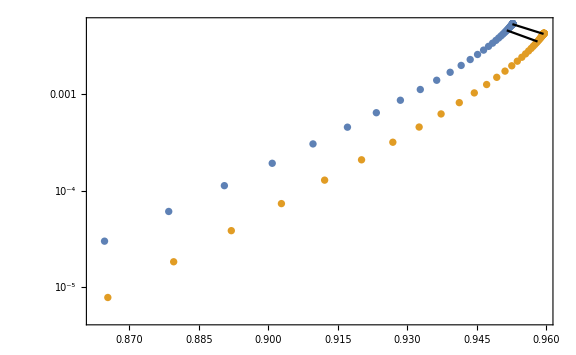

```mathematica
Show[ListLogPlot[{nsrm,nsrp},Joined->False,PlotRange->Full],ListLogPlot[{{{DataList[[24,2]]+1,DataList[[24,3]]},{DataList[[24,5]]+1,DataList[[24,6]]}},{{DataList[[41,2]]+1,DataList[[41,3]]},{DataList[[41,5]]+1,DataList[[41,6]]}}},PlotStyle->Black]]
```

```mathematica
DataList[[8]]//N
```

{5011.87,-0.0714971,0.000871181,0.0165598,-0.0674506,0.000459505,0.0133785}

```mathematica
MidNight=RGBColor["#2C3E50"]
```

RGBColor[0.17254901960784313, 0.24313725490196078, 0.3137254901960784]

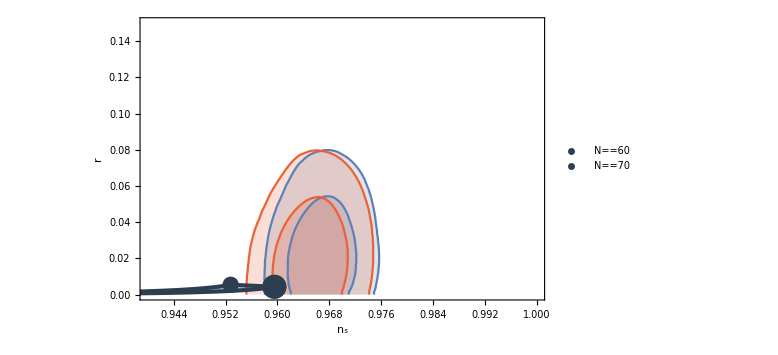

```mathematica
Show[ListPlot[{PlanckBAO2sEx,PlanckBAO1sEx,PlanckBK2sEx,PlanckBK1sEx},Filling->Bottom,PlotRange->{{0.94,1},{0,0.15}},FrameLabel->{Subscript[n, "s"],r},PlotStyle->{Color[1],Color[1],Color[4],Color[4]}],ListPlot[{nsrm,nsrp,{{-17/(6 Nms)+1,32/(9Sqrt[2])1/Nms^(3/2)},{-17/(6 Nps)+1,32/(9Sqrt[2])1/Nps^(3/2)}}},PlotStyle->{{MidNight,AbsoluteThickness[3]}},Filling->{1->{2},3->{2}}],
ListPlot[{{{-17/(6 Nms)+1,32/(9Sqrt[2])1/Nms^(3/2)}},{{-17/(6 Nps)+1,32/(9Sqrt[2])1/Nps^(3/2)}}},Joined->False,PlotStyle->{Directive[PointSize[0.02],MidNight],Directive[PointSize[0.03],MidNight]},PlotLegends->Placed[{N==Nms,N==Nps},{0.2,0.8}]]]
```

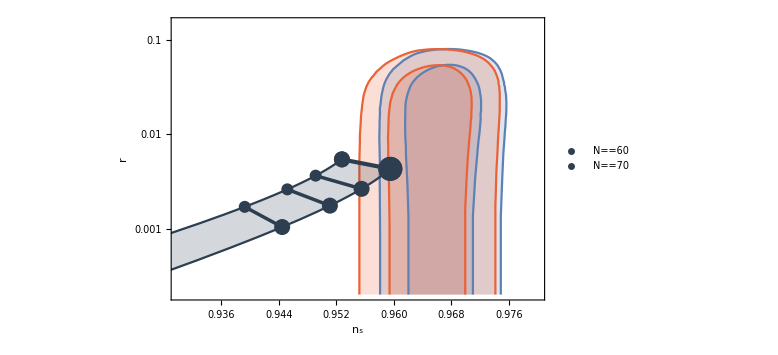

```mathematica
Show[ListLogPlot[{PlanckBAO2sEx,PlanckBAO1sEx,PlanckBK2sEx,PlanckBK1sEx},Filling->Bottom,PlotRange->{{0.93,0.98},{2 10^-4,0.15}},FrameLabel->{Subscript[n, "s"],r},PlotStyle->{Color[1],Color[1],Color[4],Color[4]}],ListLogPlot[{nsrm,nsrp,{{-17/(6 Nms)+1,32/(9Sqrt[2])1/Nms^(3/2)},{-17/(6 Nps)+1,32/(9Sqrt[2])1/Nps^(3/2)}},nsr10000,nsr20000,nsr50000(*,nsr100000*)},PlotStyle->{MidNight,MidNight,{MidNight,AbsoluteThickness[3]},{MidNight,AbsoluteThickness[2.5]},{MidNight,AbsoluteThickness[2.5]},{MidNight,AbsoluteThickness[2.5]},{MidNight,AbsoluteThickness[2.5]}},Filling->{1->{2},3->{2}}],
ListLogPlot[{{{-17/(6 Nms)+1,32/(9Sqrt[2])1/Nms^(3/2)}},{{-17/(6 Nps)+1,32/(9Sqrt[2])1/Nps^(3/2)}},{nsr10000[[1]],nsr20000[[1]],nsr50000[[1]](*,nsr100000[[1]]*)},{nsr10000[[2]],nsr20000[[2]],nsr50000[[2]](*,nsr100000[[2]]*)}},Joined->False,PlotStyle->{Directive[PointSize[0.02],MidNight],Directive[PointSize[0.03],MidNight],Directive[PointSize[0.015],MidNight],Directive[PointSize[0.02],MidNight]},PlotLegends->Placed[{N==Nms,N==Nps},{0.2,0.8}]]]
```

```mathematica
csm=Table[{DataList[[i,1]],DataList[[i,4]]},{i,Length[DataList]}];
csp=Table[{DataList[[i,1]],DataList[[i,7]]},{i,Length[DataList]}];
```

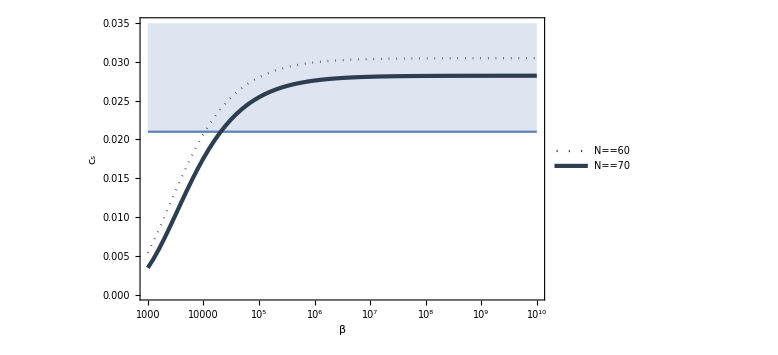

```mathematica
Show[LogLinearPlot[0.021,{x,10^3,10^10},Filling->Top,PlotRange->{{10^3,10^10},{0,0.035}},FrameLabel->{β,Subscript[c, "s"]},PlotStyle->Automatic],ListLogLinearPlot[{csm,csp},PlotStyle->{{MidNight,Dotted},{MidNight,AbsoluteThickness[3]}},PlotLegends->Placed[{N==Nms,N==Nps},{0.8,0.2}]]]
```

## O(2)

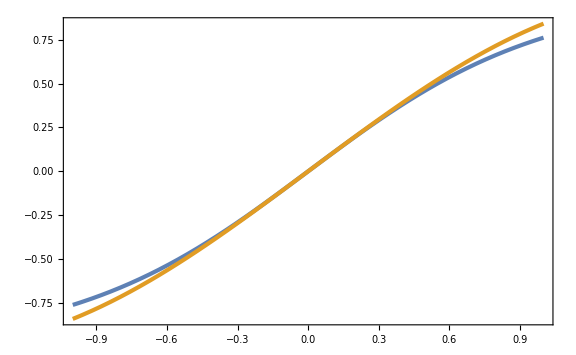

```mathematica
Plot[{Tanh[x],Sin[x]},{x,-1,1}]
```

```mathematica
P[ϕ_,X_]=-β Sin[ϕ/(√6)]X+γ^2/36 X^2;
PX[ϕ_,X_]=D[P[ϕ,X], X];
PXX[ϕ_,X_]=D[PX[ϕ,X], X];
Pϕ[ϕ_,X_]=D[P[ϕ,X], ϕ];
H[ϕ_,X_]=Sqrt[(2X PX[ϕ,X]-P[ϕ,X])/3];
dotH[ϕ_,X_]=-X PX[ϕ,X]//Simplify;
cs[ϕ_,X_]=Sqrt[PX[ϕ,X]/(PX[ϕ,X]+2X PXX[ϕ,X])];
p[ϕ_,dotϕ_,ddotϕ_]=D[PX[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]PX[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
ϵ[ϕ_,X_]=(-dotH[ϕ,X])/H[ϕ,X]^2//Simplify;
w[ϕ_,X_]=2/3 ϵ[ϕ,X]-1;
η[ϕ_,dotϕ_,ddotϕ_]=D[ϵ[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]ϵ[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
s[ϕ_,dotϕ_,ddotϕ_]=D[cs[x[t],x'[t]^2/2], t]/(H[x[t],x'[t]^2/2]cs[x[t],x'[t]^2/2])/.{x[t]->ϕ,x'[t]->dotϕ,x''[t]->ddotϕ}//Simplify;
```

```mathematica
9/2 100^2
```

45000

```mathematica
R=1;
```

```mathematica
params={β->10^5,γ->Sqrt[R]γanal[10^5]};params//N
```

{β→100000.,γ→1.65717×10^10}

```mathematica
Hanal[100]/.{γ->Sqrt[R]γanal[β]}//N
ϕanal[100]/.params//N
```

8.00937×10^-6

1.87707

```mathematica
EoMs={ϕ''[t]+3H[ϕ[t],ϕ'[t]^2/2](1+p[ϕ[t],ϕ'[t],ϕ''[t]]/3)ϕ'[t]==Pϕ[ϕ[t],ϕ'[t]^2/2]/PX[ϕ[t],ϕ'[t]^2/2],ϕ[0]==ϕanal[100],ϕ'[0]==dotϕanal[100],NN'[t]==H[ϕ[t],ϕ'[t]^2/2],NN[0]==0}/.params//Simplify;
```

```mathematica
tf=10^4 Hanal[100]^-1/.params;tf//N
```

1.24854×10^9

```mathematica
sol=NDSolve[EoMs,{ϕ[t],ϕ'[t],ϕ''[t],NN[t]},{t,0,tf}][[1]]
```

{ϕ[t]→InterpolatingFunction[…][t],ϕ'[t]→InterpolatingFunction[…][t],ϕ''[t]→InterpolatingFunction[…][t],NN[t]→InterpolatingFunction[…][t]}

```mathematica
Mpl=2.435 10^18;
```

```mathematica
ϕsol[t_]=ϕ[t]/.sol;
dotϕsol[t_]=ϕ'[t]/.sol;
ddotϕsol[t_]=ϕ''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[ϕsol[t],dotϕsol[t]^2/2]/.params;
ϵsol[t_]=ϵ[ϕsol[t],dotϕsol[t]^2/2]/.params;
wsol[t_]=w[ϕsol[t],dotϕsol[t]^2/2]/.params;
ηsol[t_]=η[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
ssol[t_]=s[ϕsol[t],dotϕsol[t],ddotϕsol[t]]/.params;
cssol[t_]=cs[ϕsol[t],dotϕsol[t]^2/2]/.params;
calPsol[t_]=1/(2ϵsol[t] cssol[t])(Hsol[t]/(2π))^2;
nsm1sol[t_]=-2ϵsol[t]-ηsol[t]-ssol[t];
rsol[t_]=16ϵsol[t]cssol[t];
```

```mathematica
tend=t/.FindRoot[ϵsol[t]==1,{t,100 Hanal[100]^-1/.params}]
```

3.23126×10^7

```mathematica
Nend=Nsol[tend]
```

98.5863

```mathematica
Npivot=Nend-70
```

28.5863

```mathematica
tpivot=t/.FindRoot[Nsol[t]==Npivot,{t,20 Hanal[100]^-1/.params}]
```

4.30884×10^6

```mathematica
nsm1sol[tpivot]+1
rsol[tpivot]
cssol[tpivot]
```

0.957815

0.00361234

0.0266156

```mathematica
R=calPsol[tpivot]/(2 10^-9)
```

1.

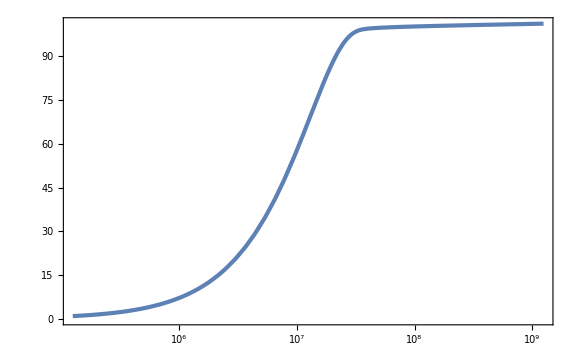

```mathematica
LogLinearPlot[Nsol[t],{t,Hanal[100]^-1/.params,tf}]
```

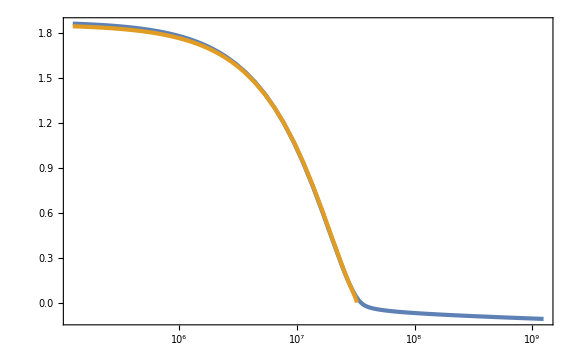

```mathematica
LogLinearPlot[{ϕsol[t],ϕanal[Nend-Nsol[t]]/.params},{t,Hanal[100]^-1/.params,tf}]
```

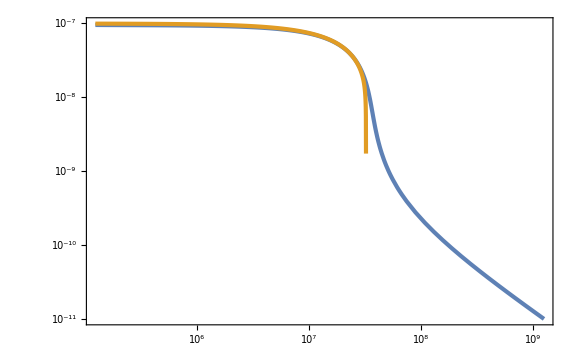

```mathematica
LogLogPlot[{-dotϕsol[t],-dotϕanal[Nend-Nsol[t]]/.params},{t,Hanal[100]^-1/.params,tf},PlotRange->Full]
```

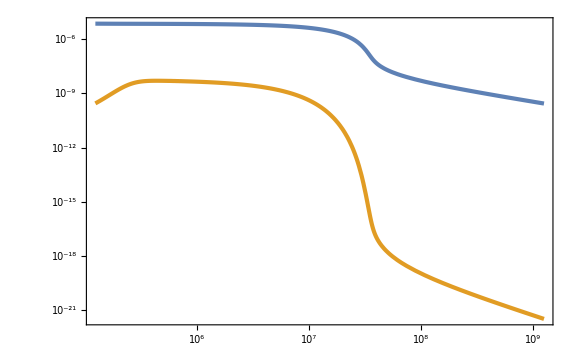

```mathematica
LogLogPlot[{Hsol[t],calPsol[t]},{t,Hanal[100]^-1/.params,tf}]
```

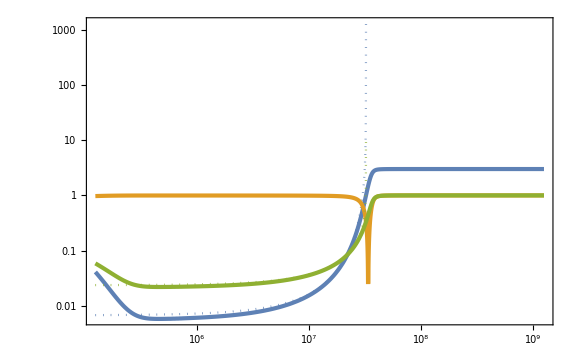

```mathematica
LogLogPlot[{ϵsol[t],ϵanal[Nend-Nsol[t]]/.params,Abs[wsol[t]],cssol[t],csanal[Nend-Nsol[t]]/.params},{t,Hanal[100]^-1/.params,tf},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[3],AbsoluteThickness[3]},{Color[3],Dotted}}]
```

```mathematica
wList=Select[Table[{Nsol[t],wsol[t]},{t,0,tf,Hanal[100]^-1/.params}],#[[1]]>90&];
```

```mathematica
fitparam=FindFit[wList,Tanh[(2(x-a))/b],{{a,100},{b,1}},x]
```

{a→98.7939,b→1.02794}

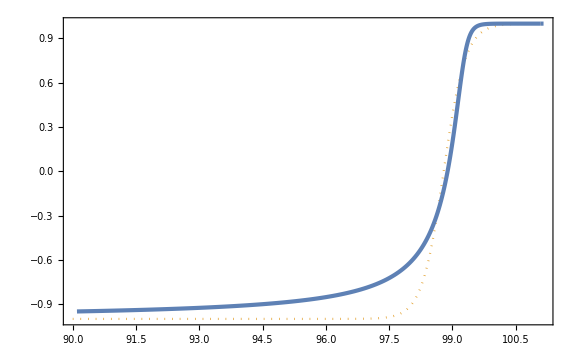

```mathematica
Show[Plot[Tanh[(2(x-a))/b]/.fitparam,{x,90,Nsol[tf]},PlotStyle->{Color[2],Dotted}],ListPlot[wList,PlotRange->Full]]
```

```mathematica
LogHList=Select[Table[{Nsol[t],Log10[Hsol[t]]},{t,0,tf,Hanal[100]^-1/.params}],#[[1]]>90&];
```

```mathematica
Hfit[NN_]=Log10[Exp[-3/2(NN-a+b/2(Log[Cosh[2(NN-a)/b]]+Log[2]))]]+log10H0/.fitparam//Simplify
```

log10H0+Log[(1.33778×10^64 ⅇ^(-3 NN/2))/Cosh[192.217-1.94564 NN]^0.770955]/Log[10]

```mathematica
H0fit=FindFit[LogHList,Hfit[NN],log10H0,NN]
```

{log10H0→-6.47336}

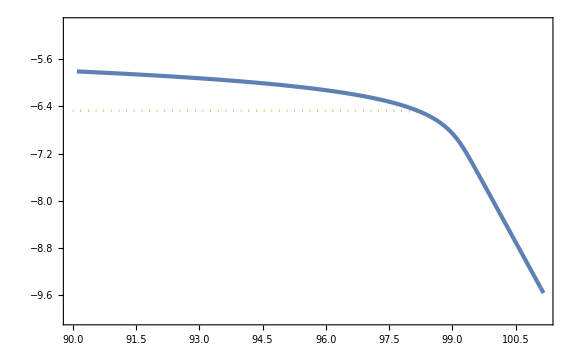

```mathematica
Show[Plot[Hfit[NN]/.H0fit,{NN,90,Nsol[tf]},PlotStyle->{Color[2],Dotted},PlotRange->{-10,-5}],ListPlot[LogHList,PlotRange->Full]]
```

```mathematica
H0dt=NIntegrate[10^(Hfit[NN]-log10H0)/.fitparam,{NN,a-b/.fitparam,a+b/.fitparam}]
```

1.13369

```mathematica
Ts=(2 30^(1/4))/Sqrt[3π] 1/106.75^(1/2)0.02 10^(2log10H0)Mpl/.H0fit
```

812.447

```mathematica
67.3-Log[0.002/(67.4 10^3/299792458)]+1/3 Log[rsol[tpivot]/0.12]-1/3 Log[Ts/10^9]-1/12 Log[106.75]
```

68.2319